## Load Radia

```mathematica
ClearAll["Global`*"]
<<Radia`;
RadPlot3DOptions[];
radUtiDelAll[]; (*Erase all previous elements*)
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

## Functions

### BlockGeometry

```mathematica
idBlockGeometry[checkgeo_]:=(
Module[{geo1,geo2,geo3},

(*Geo A1, Delta 52.5*)
If[checkgeo==1,
geo1={{-21.5,-50},{21.5,-50},{22.5,-49},{22.5,-41.8},{16.794,-37.654},{-16.794,-37.654},{-22.5,-41.8},{-22.5,-49}};
geo2={{16.794,-37.654},{16.794,-33.946},{-16.794,-33.946},{-16.794,-37.654}};
geo3={{16.794,-33.946},{22.5,-29.8},{22.5,-19.3},{5.25,0.0},{-5.25,0.0},{-22.5,-19.3},{-22.5,-29.8},{-16.794,-33.946}};
];

If[checkgeo==2,
geo1={{16.794,-37.654},{16.794,-33.946},{-16.794,-33.946},{-16.794,-37.654}};
geo2={{16.794,-33.946},{22.5,-29.8},{22.5,-19.3},{5.25,0.0},{-5.25,0.0},{-22.5,-19.3},{-22.5,-29.8},{-16.794,-33.946}};
];

Return[{geo1,geo2,geo3}]
];
)
```

### cassetteDraw

```mathematica
cassetteDraw::usage = "magnetizations = Lista das magnetizações dos blocos de um cassete (lista de tamanho n); blockGeo = {geo1,geo2,geo3}; 
termination = {{lista de magnetizacoes na entrada}, {lista de espessuras na entrada}, {lista de espaçamentos na entrada},{lista de magnetizacoes na saída}, {lista de espessuras na saída}, {lista de espaçamentos na saída}}"; 


idCassetteDraw[magnetizations_,blockGeo_,posErrors_,termination_,periodL_,blockThick_,gap_,blockGap_,subdiv_]:=(
Module[{cassette,block,obj,obj1,obj2,obj3,blocknumber,vacodym745ap,termLength,i,j,parts,randomErrorY,randomErrorZ,longPos},

cassette=radObjCnt[{}];
parts=Length[blockGeo];
obj=ConstantArray[{},parts];
blocknumber=Length[magnetizations]+Length[termination[[1]]]+Length[termination[[4]]];

(*Position Errors*)
If[posErrors[[1]]>0,
randomErrorY=Table[RandomVariate[NormalDistribution[posErrors[[1]]/2,(posErrors[[1]]/2)/3]],{i,1,blocknumber}]*RandomChoice[{-1,1},blocknumber];
,
randomErrorY=ConstantArray[0,blocknumber];
];
If[posErrors[[2]]>0,
randomErrorZ=Table[RandomVariate[NormalDistribution[posErrors[[2]]/2,(posErrors[[2]]/2)/3]],{i,1,blocknumber}]*RandomChoice[{-1,1},blocknumber];
,
randomErrorZ=ConstantArray[0,blocknumber];
];

(*===== Termination Front =====*)
block=ConstantArray[{},Length[termination[[1]]]];

For[i=1,i≤ Length[termination[[1]]],i++,
block[[i]]=radObjCnt[{}];

(*Next Block Position*)
If[i≤1,
longPos=0,
longPos=longPos+0.5*termination[[2,i-1]]+termination[[3,i-1]]+0.5*termination[[2,i]];
];

(*Create the Block Object*)
For[j=1,j≤ parts,j++,
(*Extrude part*)
obj[[j]]=radObjThckPgn[longPos,termination[[2,i]],blockGeo[[j]],termination[[1,i]]];
(*Part Subdivision*)
radObjDivMag[obj[[j]],subdiv[[j]]];
(*Add Part to block*)
radObjAddToCnt[block[[i]],{obj[[j]]}];
];

(*Position Error*)
radTrfOrnt[block[[i]],radTrfTrsl[{0,randomErrorY[[i]],randomErrorZ[[i]]}]];

(*Apply Material and Magnetization*)
vacodym745ap=radMatLin[{0.06,0.17},termination[[1,i]]];
radMatApl[block[[i]],vacodym745ap];

(*Add to Cassette*)
radObjAddToCnt[cassette,{block[[i]]}];
];

(*===== Periods =====*)
block=ConstantArray[{},Length[magnetizations]];

For[i=1,i≤ Length[magnetizations],i++,
block[[i]]=radObjCnt[{}];

(*Block Position*)
If[i≤1,
longPos=longPos+0.5*termination[[2,-1]]+termination[[3,-1]]+0.5*blockThick;
,
longPos=longPos+blockThick+blockGap;
];

For[j=1,j≤ parts,j++,
obj[[j]]=radObjThckPgn[longPos,blockThick,blockGeo[[j]],magnetizations[[i]]];
(*Part Subdivision*)
radObjDivMag[obj[[j]],subdiv[[j]]];
(*Add Part to block*)
radObjAddToCnt[block[[i]],{obj[[j]]}];
];

(*Position Error*)
radTrfOrnt[block[[i]],radTrfTrsl[{0,randomErrorY[[i]],randomErrorZ[[i]]}]];

(*Apply Material and Magnetization*)
vacodym745ap=radMatLin[{0.06,0.17},magnetizations[[i]]];
radMatApl[block[[i]],vacodym745ap]; 

(*Add to Cassette*)
radObjAddToCnt[cassette,{block[[i]]}];

];

(*===== Termination Back =====*)
block=ConstantArray[{},Length[termination[[1]]]];

For[i=1,i≤ Length[termination[[4]]],i++,
block[[i]]=radObjCnt[{}];

(*Next Block Position*)
If[i≤ 1,
longPos=longPos+blockThick/2+termination[[6,1]]+termination[[5,1]]/2;
,
longPos=longPos+0.5*termination[[5,i-1]]+termination[[6,i]]+0.5*termination[[5,i]];
];

For[j=1,j≤ parts,j++,
obj[[j]]=radObjThckPgn[longPos,termination[[5,i]],blockGeo[[j]],termination[[4,i]]];
(*Part Subdivision*)
radObjDivMag[obj[[j]],subdiv[[j]]];
(*Add Part to block*)
radObjAddToCnt[block[[i]],{obj[[j]]}];
];

(*Position Error*)
radTrfOrnt[block[[i]],radTrfTrsl[{0,randomErrorY[[i]],randomErrorZ[[i]]}]];

(*Apply Material and Magnetization*)
vacodym745ap=radMatLin[{0.06,0.17},termination[[4,i]]];
radMatApl[block[[i]],vacodym745ap]; 

(*Add to Cassette*)
radObjAddToCnt[cassette,{block[[i]]}];

];

Return[cassette]
];
)
```

### IDDraw

```mathematica
idDraw[typeID_,gap_,nPeriods_,periodL_,blockGeo_,blockThick_,blockGap_,magnetizations_,terminations_,mode_,subdiv_ ,posErrors_ :{0,0},gap2_ :0]:=(
Module[{device,cassette,mag,cassetteD,modeslist,phase,i,displacement,cassPos},
device=radObjCnt[{}];
cassette=ConstantArray[{},4];

(*==== Generate Cassettes =====*)
For[i=1,i≤Length[magnetizations],i++,
cassette[[i]]=idCassetteDraw[magnetizations[[i]],blockGeo,posErrors,terminations[[i]],periodL,blockThick,gap,blockGap,subdiv];

(*Apply Gap*)
radTrfOrnt[cassette[[i]],radTrfTrsl[{0,0,-gap/2}]];

If[typeID=="DeltaUndulator",
(*Apply Phase*)
modeslist={{0,0,0,0},{-1/4,0,-1/4,0},{-1/2,0,-1/2,0},{-1/4,0,1/4,0},{-1/4,-1/4,0,0},{-1/4,0,0,-1/4}}*periodL;
phase=modeslist[[mode]];
radTrfOrnt[cassette[[i]],radTrfTrsl[{phase[[i]],0,0}]];

(*Apply Rotation*)
radTrfOrnt[cassette[[i]],radTrfRot[{0,0,0},{1,0,0},(i-1)*Pi/2]];
];

If[typeID=="PlanarUndulator",
(*Apply Phase*)
modeslist={{0,0},{0,-1/2},{0,-1/4},{0,1/2},{0,1/4}}*periodL;
phase=modeslist[[mode]];
radTrfOrnt[cassette[[i]],radTrfTrsl[{phase[[i]],0,0}]];

(*Apply Rotation*)
radTrfOrnt[cassette[[i]],radTrfRot[{0,0,0},{1,0,0},(i-1)*Pi]];
];

If[typeID=="EPU",
(*Apply Phase*)
modeslist={{0,0,0,0},{-1/4,0,-1/4,0},{-1/2,0,-1/2,0},{-1/4,0,1/4,0}}*periodL;
phase=modeslist[[mode]];
radTrfOrnt[cassette[[i]],radTrfTrsl[{phase[[i]],0,0}]];

(*Apply Position*)
zdesloc=gap+50/2; ydesloc=gap2+22; a=Min[Flatten[blockGeo,1][[All,2]]];
cassPos={{0,-ydesloc,0},{0,ydesloc,0},{0,ydesloc,2*zdesloc},{0,-ydesloc,2*zdesloc}};

radTrfOrnt[cassette[[i]],radTrfTrsl[cassPos[[i]]]];
];


radObjAddToCnt[device,{cassette[[i]]}];
];

If[typeID=="DeltaUndulator",
(*Rotate ID*)
radTrfOrnt[device,radTrfRot[{0,0,0},{1,0,0},-Pi/4]];
];

(*Adjust Axis*)
device=radTrfOrnt[device,radTrfRot[{0,0,0},{0,1,0},-Pi/2]];
device=radTrfOrnt[device,radTrfRot[{0,0,0},{0,0,1},-Pi/2]];

Return[device];
];
)
```

### Generate Block Mag

```mathematica
idGenerateMag[typeID_,nPeriods_,periodL_,blockThick_,blockGap_,symmetry_,magnAmp_,magError_ :0,magAmpError_ :0.02,magTheta_ :1]:=(
Module[{mag,magnetization,j,i,termination,phi,theta,dmag},

(*===== ID Type =====*)
If[typeID=="DeltaUndulator",
mag={{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};
];

If[typeID=="PlanarUndulator",
mag={{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};
];

If[typeID=="EPU",
mag={{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{magnAmp,0,0},{0,0,-magnAmp},{-magnAmp,0,0},{0,0,magnAmp}},{{magnAmp,0,0},{0,0,-magnAmp},{-magnAmp,0,0},{0,0,magnAmp}}};
];

(*===== Create Cassette Magnetizations =====*)
magnetization=ConstantArray[{},Length[mag]];

For[j=1,j≤ Length[mag],j++,
magnetization[[j]]=Nest[Join[mag[[j]],#,1]&,mag[[j]],(nPeriods-1)];
If[symmetry=="symmetric",
magnetization[[j]]=Delete[magnetization[[j]],-1];
,
magnetization[[j]]=Join[magnetization[[j]],{magnetization[[j,1]]}];
];
];

(*===== Generate Errors =====*)
phi=RandomReal[{0,2*Pi},Length[Flatten[magnetization,1]]];
phi=ArrayReshape[phi,{Length[magnetization],Length[magnetization[[1]]]}];

theta=Table[RandomVariate[NormalDistribution[0,(magTheta*Pi/180)/3]],{i,1,Length[Flatten[magnetization,1]]}];
theta=ArrayReshape[theta,{Length[magnetization],Length[magnetization[[1]]]}]; 

If[magError≥1,
dmag=1+Table[RandomVariate[NormalDistribution[0,magAmpError/3]],{i,1,Length[Flatten[magnetization,1]]}];
dmag=ArrayReshape[dmag,{Length[magnetization],Length[magnetization[[1]]]}]; 
,
dmag=ConstantArray[1,{Length[magnetization],Length[magnetization[[1]]]}];
phi=phi*0;
theta=theta*0;
];

(*===== Apply Errors =====*)
For[i=1,i≤ Length[magnetization],i++,
magnetization[[i]]=magnetization[[i]]*dmag[[i]];

For[j=1,j≤ Length[magnetization[[1]]],j++,
If[Mod[j,2]≤0,
magnetization[[i,j]]=RotationMatrix[phi[[i,j]],{0,0,1}].RotationMatrix[theta[[i,j]],{0,1,0}].magnetization[[i,j]];
,
magnetization[[i,j]]=RotationMatrix[phi[[i,j]],{1,0,0}].RotationMatrix[theta[[i,j]],{0,1,0}].magnetization[[i,j]];
];
]

];
Return[magnetization]
];
)
```

### GenerateTermination Mag

```mathematica
idGenerateTerm[termType_,blockThick_,blockGap_,periodL_,magnAmp_,magFront_ :{{}},magBack_ :{{}}]:=(
Module[{termination,termMagFront,termMagBack,termBlockThick,termBlockGap},

(*----- ThreeBlocksAntiSym Termination -----*)
If[termType=="ThreeBlocksAntiSym",
If[Length[magFront[[1]]]≥ 3,
termMagFront=magFront;
,
termMagFront={{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};
];

If[Length[magBack[[1]]]≥ 3,
termMagBack=magBack;
,
termMagBack={{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};
];

termBlockThick={1/4,1/2,3/4}*blockThick;
termBlockGap={0.875*periodL/4-((0.25+0.5)/2*blockThick),0.875*periodL/4-((0.5+0.75)/2*blockThick),0.875*periodL/4-((0.75+1)/2*blockThick)};

termination=Table[{termMagFront[[i]],termBlockThick,termBlockGap,termMagBack[[i]],Reverse[termBlockThick],Reverse[termBlockGap]},{i,1,Length[termMagFront]}];
];

(*----- ThreeBlocksAntiSymReal -----*)
If[termType=="ThreeBlocksAntiSymReal",

If[Length[magFront[[1]]]≥ 6,
termMagFront=magFront;
,
termMagFront={{{0,0,magnAmp},{-magnAmp,0,0},{-magnAmp,0,0},{0,0,-magnAmp},{0,0,-magnAmp},{0,0,-magnAmp}},{{0,0,magnAmp},{-magnAmp,0,0},{-magnAmp,0,0},{0,0,-magnAmp},{0,0,-magnAmp},{0,0,-magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{magnAmp,0,0},{0,0,magnAmp},{0,0,magnAmp},{0,0,magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{magnAmp,0,0},{0,0,magnAmp},{0,0,magnAmp},{0,0,magnAmp}}};
];

If[Length[magBack[[1]]]≥ 6,
termMagBack=magBack;
,
termMagBack={{{0,0,magnAmp},{0,0,magnAmp},{0,0,magnAmp},{-magnAmp,0,0},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,magnAmp},{0,0,magnAmp},{0,0,magnAmp},{-magnAmp,0,0},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,-magnAmp},{0,0,-magnAmp},{0,0,-magnAmp},{magnAmp,0,0},{magnAmp,0,0},{0,0,magnAmp}},{{0,0,-magnAmp},{0,0,-magnAmp},{0,0,-magnAmp},{magnAmp,0,0},{magnAmp,0,0},{0,0,magnAmp}}};
];

termBlockThick=ConstantArray[0.25,6]*blockThick;
termBlockGap={0.875*periodL/4-((0.25+0.5)/2*blockThick),0.0,0.875*periodL/4-((0.5+0.75)/2*blockThick),0.0,0.0,0.875*periodL/4-((0.75+1)/2*blockThick)};

termination=Table[{termMagFront[[i]],termBlockThick,termBlockGap,termMagBack[[i]],Reverse[termBlockThick],Reverse[termBlockGap]},{i,1,Length[termMagFront]}];
];

(*----- FourBlocksAntiSym -----*)
If[termType=="FourBlocksAntiSym",

If[Length[magFront[[1]]]≥ 4,
termMagFront=magFront;
,
termMagFront={{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};
];

If[Length[magBack[[1]]]≥ 4,
termMagBack=magBack;
,
termMagBack={{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0}}};
];

termBlockThick={3.25,3.25,9.75,9.75};
termBlockGap={8.7,2.0,3.3,1.0};

termination=Table[{termMagFront[[i]],termBlockThick,termBlockGap,termMagBack[[i]],Reverse[termBlockThick],Reverse[termBlockGap]},{i,1,Length[termMagFront]}];
];

(*----- FourBlocksAntiSymReal -----*)
If[termType=="FourBlocksAntiSymReal",

If[Length[magFront[[1]]]≥ 8,
termMagFront=magFront;
,
termMagFront={{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{-magnAmp,0,0},{-magnAmp,0,0},{0,0,-magnAmp},{0,0,-magnAmp},{0,0,-magnAmp}},{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{-magnAmp,0,0},{-magnAmp,0,0},{0,0,-magnAmp},{0,0,-magnAmp},{0,0,-magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{magnAmp,0,0},{magnAmp,0,0},{0,0,magnAmp},{0,0,magnAmp},{0,0,magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{magnAmp,0,0},{magnAmp,0,0},{0,0,magnAmp},{0,0,magnAmp},{0,0,magnAmp}}};
];

If[Length[magBack[[1]]]≥ 8,
termMagBack=magBack;
,
termMagBack={{{0,0,magnAmp},{0,0,magnAmp},{0,0,magnAmp},{-magnAmp,0,0},{-magnAmp,0,0},{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0}},{{0,0,magnAmp},{0,0,magnAmp},{0,0,magnAmp},{-magnAmp,0,0},{-magnAmp,0,0},{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0}},{{0,0,-magnAmp},{0,0,-magnAmp},{0,0,-magnAmp},{magnAmp,0,0},{magnAmp,0,0},{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0}},{{0,0,-magnAmp},{0,0,-magnAmp},{0,0,-magnAmp},{magnAmp,0,0},{magnAmp,0,0},{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0}}};
];

termBlockThick=ConstantArray[3.25,8];
termBlockGap={8.7,2,0,0,3.3,0,0,1};

termination=Table[{termMagFront[[i]],termBlockThick,termBlockGap,termMagBack[[i]],Reverse[termBlockThick],Reverse[termBlockGap]},{i,1,Length[termMagFront]}];
];


(*----- Three Blocks Symmetric Termination -----*)
If[termType=="ThreeBlockSym",
If[Length[magFront[[1]]]≥ 3,
termMagFront=magFront;
,
termMagFront={{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};
];

If[Length[magBack[[1]]]≥ 3,
termMagBack=magBack;
,
termMagBack={{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}}};
];

termBlockThick={1/4,1/2,3/4}*blockThick;
termBlockGap={0.875*periodL/4-((0.25+0.5)/2*blockThick),0.875*periodL/4-((0.5+0.75)/2*blockThick),0.875*periodL/4-((0.75+1)/2*blockThick)};

termination=Table[{termMagFront[[i]],termBlockThick,termBlockGap,termMagBack[[i]],Reverse[termBlockThick],Reverse[termBlockGap]},{i,1,Length[termMagFront]}];
];

(* ----- Simple Half Block Termination -----*)
If[termType=="Simple-Half",
termination={{{0,0,magnAmp}},{1/2}*blockThick,{blockGap},{{0,0,magnAmp}},{1/2}*blockThick,{blockGap}};
];

Return[termination]
];
)
```

### Sorting Import Mag

```mathematica
idSortingImportMag[fileName_ :"Magnetizations.xlsx",headLine_ :0]:=(
Module[{dir,M,file,listMag0,listMag},
dir=NotebookDirectory[];
(*fileName="Magnetizations.xlsx";*)
file=StringJoin[dir,fileName];
M=Import[file];

M=Flatten[M,1];
listMag0=Join[{M[[headLine+1;;-1,5]],M[[headLine+1;;-1,7]],M[[headLine+1;;-1,8]],M[[headLine+1;;-1,9]]},2];

listMag=Table[{{listMag0[[2,i]],listMag0[[3,i]],listMag0[[4,i]]},listMag0[[1,i]]},{i,1,Length[listMag0[[1]]]}];

Return[listMag]
];
)
```

### Sorting Export Mag

```mathematica
idExportMag[listMag_,expFileName_ :"Magnetizations.xlsx"]:=(
Module[{dir,exportMtx},
dir=NotebookDirectory[];
exportMtx=Table[Join[{{},{},{},StringJoin["B-",ToString[i]]},Flatten[listMag[[i,1;;-2]]]],{i,1,Length[listMag]}];
Export[StringJoin[dir,expFileName],exportMtx];
];
)
```

### Solve

```mathematica
idSolve[device_,randomization_ :{1*^-9,1*^-9,1*^-9}]:=(
Module[{abs,rel,zero,re,t0,t1},

radFldLenTol[randomization[[1]],randomization[[2]],randomization[[3]]];

re=RadSolve[device,1*^-9,10000];
]
)
```

### Field Calc

```mathematica
idField[undulator_,li_,lf_,lNpts_,{posV_,posH_},display_,oneplot_]:=(
Module[{lstep,t0,t1,baxis,btotal,axispoints,plot},
lstep=(lf-li)/lNpts;
t0=AbsoluteTime[];

(*----- Axis Field Calc -----*)
baxis=Table[radFld[undulator,"b",{posH,posV,z}],{z,li,lf-lstep,lstep}];

t1=AbsoluteTime[];
(*Print["> Field Components: (elapsed time: ",t1-t0 ,"[s])"];*)

(*----- Plots -----*)
If[display≥ 1,
plot=ConstantArray[{},3];
(*Axis Plot*)
axispoints=Table[li+(n-1)*lstep,{n,1,lNpts}];
plot[[1]]=ListLinePlot[Table[{axispoints[[i]],baxis[[i,1]]},{i,1,lNpts}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Magnetic Field [T]",12]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLegends->Placed[{"Bx"},Above]];
plot[[2]]=ListLinePlot[Table[{axispoints[[i]],baxis[[i,2]]},{i,1,lNpts}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Magnetic Field [T]",12]},PlotTheme->"Detailed",PlotStyle->{Orange},ImageSize->Medium,PlotRange->All,PlotLegends->Placed[{"By"},Above]];
plot[[3]]=ListLinePlot[Table[{axispoints[[i]],baxis[[i,3]]},{i,1,lNpts}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Magnetic Field [T]",12]},PlotTheme->"Detailed",PlotStyle->{Green},ImageSize->Medium,PlotRange->All,PlotLegends->Placed[{"Bz"},Above]];

If[oneplot≥1,
maxims=Table[{i,Max[baxis[[All,i]]]},{i,1,3}];
plotOrder=SortBy[maxims,Last];
Print[Show[Table[plot[[plotOrder[[-i,1]]]],{i,1,3}]]];
,
Print[GraphicsRow[{plot[[1]],plot[[2]],plot[[3]]},Spacings->{0,10},ImageSize->{1200,300},AspectRatio->Full]];
];
];

Return[baxis]
];
)
```

### Field Integral

```mathematica
idFieldInt[undulator_,li_,lf_,lstep_,baxis_,display_,oneplot_]:=(
Module[{i,dz,area,area2,integral,integral2,firstInt,secondInt,axispoints,plot,t0,t1},
(*----- First Integral -----*)
t0=AbsoluteTime[];
dz=lstep;

area=Table[{(baxis[[i,1]]+baxis[[i+1,1]])/2*dz,(baxis[[i,2]]+baxis[[i+1,2]])/2*dz,(baxis[[i,3]]+baxis[[i+1,3]])/2*dz},{i,1,Length[baxis]-1}];
integral=Accumulate[area]; (*T.mm*)
firstInt=integral*10^4/10 ;(*G.cm*)

(*----- Second Integral -----*)
area2=Table[{(integral[[i,1]]+integral[[i+1,1]])/2*dz,(integral[[i,2]]+integral[[i+1,2]])/2*dz,(integral[[i,3]]+integral[[i+1,3]])/2*dz},{i,1,Length[integral]-1}];
integral2=Accumulate[area2];(*T.mm.b2*)
secondInt=(integral2*10^4/100)/1000; (*kG.cm.b2*)

t1=AbsoluteTime[];

(*Print["> Field Integrals: elapsed time = ",(t1-t0)," [s]"];*)

(*Print["First integrals : ", firstInt[[-1]]," [G.cm]"];
Print["Second integrals : ", secondInt[[-1]]," [kG.cm.b2]"];*)

(*----- Plots -----*)
If[display≥ 1,
plot=ConstantArray[{},3];
axispoints=Table[(li+lstep/2)+(n-1)*lstep,{n,1,Length[baxis]-1}];

plot[[1]]=ListLinePlot[Table[{axispoints[[i]],firstInt[[i,1]]},{i,1,Length[firstInt]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Field Integral [G.cm]",12]},PlotTheme->"Detailed",ImageSize->Medium,PlotLegends->Placed[{"Bx"},Above]];
plot[[2]]=ListLinePlot[Table[{axispoints[[i]],firstInt[[i,2]]},{i,1,Length[firstInt]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Field integral [G.cm]",12]},PlotTheme->"Detailed",PlotStyle->{Orange},ImageSize->Medium,PlotLegends->Placed[{"By"},Above]];
plot[[3]]=ListLinePlot[Table[{axispoints[[i]],firstInt[[i,3]]},{i,1,Length[firstInt]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Field integral [G.cm]",12]},PlotTheme->"Detailed",PlotStyle->{Green},ImageSize->Medium,PlotLegends->Placed[{"Bz"},Above]];

If[oneplot≥1,
maxims=Table[{i,Max[firstInt[[All,i]]]},{i,1,3}];
plotOrder=SortBy[maxims,Last];
Print[Show[Table[plot[[plotOrder[[-i,1]]]],{i,1,3}]]];
,
Print[GraphicsRow[plot,Spacings->{0,10},ImageSize->{1200,300},AspectRatio->Full]];
];
];

Return[{firstInt,secondInt}]
];
)
```

### Trajectory - RungeKutta4

```mathematica
idTrajectory::usage = "IDRungeKuttaTrajectory[device, energy, r0, smax, rkstep]: Calculates the particle trajectory using the Runge-Kutta algorithm. The particle energy must be in GeV, r0 is the initial position and normalized momentum vector {x0, y0, z0, dx0ds, dy0ds, dz0ds}, smax and rkstep are the final longitudinal position and the Runge-Kutta step. All positions are in millimeters.";

idTrajectory[device_, energy_,r0_,smax_,rkstep_,display_] := Module[
{trajectory, ElectronRestEnergy, LightSpeed, beta, brho, a, b, b1, b2, b3, r,rp, r1, r2, r3, drds1, drds2, drds3, drds4, i, sm, step, t0, t1,p1,p2},

t0=AbsoluteTime[];

ElectronRestEnergy=510998.92811; (*[eV]*)
LightSpeed=299792458;(*[m/s]*)

beta=Sqrt[1.0-(1.0/((energy*1000000000/ElectronRestEnergy)^2))];
brho=(beta*energy*1000000000/LightSpeed);
a=1.0/brho;

r1 = {0,0,0,0,0,0};
r2 = {0,0,0,0,0,0};
r3 = {0,0,0,0,0,0};
r= r0;

(*from mm to m*)
r[[1]]= r[[1]]/1000; r[[2]]= r[[2]]/1000; r[[3]]= r[[3]]/1000;
sm = smax/1000;
step = rkstep/1000;

trajectory={};
AppendTo[trajectory, {r[[1]]*1000, r[[2]]*1000, r[[3]]*1000, r[[4]], r[[5]], r[[6]]}];

While [r[[3]]<sm,
rp =r;
b=radFld[device, "BxByBz", 1000*rp[[;;3]]];
	drds1=auxIDNewtonLorentzEquation[a,r,b];
r1=rp+(step/2.0)*drds1;

b1=radFld[device, "BxByBz", 1000*r1[[;;3]]];
	drds2=auxIDNewtonLorentzEquation[a,r1,b1];
r2=rp+(step/2.0)*drds2;

b2=radFld[device, "BxByBz", 1000*r2[[;;3]]];
drds3=auxIDNewtonLorentzEquation[a,r2,b2];
r3=rp+step*drds3;

b3=radFld[device, "BxByBz", 1000*r3[[;;3]]];
drds4=auxIDNewtonLorentzEquation[a,r3,b3];
r=rp+(step/6.0)*(drds1+2.0*drds2+2.0*drds3+drds4);

AppendTo[trajectory, {r[[1]]*1000, r[[2]]*1000, r[[3]]*1000, r[[4]], r[[5]], r[[6]]}];
];

t1=AbsoluteTime[];
(*Print["> IDRungeKuttaTrajectory: elapsed time = ",(t1-t0)," s"];*)

If[display≥ 1,
(*Plots*)
p1=ListLinePlot[Table[{trajectory[[i,3]],trajectory[[i,1]]},{i,1,Length[trajectory]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["X [mm]",12]},PlotLabel->Style["X Direction Trajectory",Bold,12],PlotTheme->"Detailed",ImageSize->Medium];
p2=ListLinePlot[Table[{trajectory[[i,3]],trajectory[[i,2]]},{i,1,Length[trajectory]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Y [mm]",12]},PlotLabel->Style["Y Direction Trajectory",Bold,12],PlotTheme->"Detailed",ImageSize->Medium];

Print[Row[{p1,p2},"\t\t"]];
];

Return[trajectory];
];
```

### AuxRungeKutta

```mathematica
auxIDNewtonLorentzEquation[a_,r_,b_]:=Module[
{drds},
drds = {0,0,0,0,0,0};
drds[[1]]=r[[4]];
drds[[2]]=r[[5]];
drds[[3]]=r[[6]];
drds[[4]]=-a*(r[[5]]*b[[3]]-r[[6]]*b[[2]]);
drds[[5]]=-a*(r[[6]]*b[[1]]-r[[4]]*b[[3]]);
drds[[6]]=-a*(r[[4]]*b[[2]]-r[[5]]*b[[1]]);
Return[drds];
];
```

### PhaseError - RungeKutta

```mathematica
idPhaseError[baxis_,xo_,xf_,nx_,Trajetoria_,eEnergy_]:=(
Module[{eletron,mo,eRestEnergy,bfield,bfieldT,longAxis,ampX,ampY,ampZ,ampT,peakX,peakY,peakZ,peakT,longPeak,longPeakX,longPeakY,longPeakZ,longPeakT,periods,nperiods,periodL,kparam,gamma,lambda,intField0,intField,drop,phaseError,phase,j,jmin,rmsError,fitData,fitLin,linearFit,linearizedPhase,p3,a,b,I00,I0,p0,btotal,dx,c,s,errorP,t0,t1},
t0=AbsoluteTime[];

(*Check Inputs*)
If[Length[baxis≠ Length[Trajetoria]],Return["[ERROR] : Field vector and Trajectory Vector have not the same lenght."]];
If[eEnergy>100,Return["[ERROR] : Electron beam energy to high. Check if the input energy is in Gev."]];

(*Total Field*)
btotal=Sqrt[baxis[[All,1]]^2+baxis[[All,2]]^2+baxis[[All,3]]^2];

(*===== Parameters =====*)
eletron=1.60217662*^-19; mo=9.10938356*^-31;
eRestEnergy=510998.92811; (*[eV]*) (* == mo*c^2[J]*)
c=299792458; (*m/s*)

bfield=baxis;
bfieldT=btotal;

(*Principal Longitudinal Axis*)
dx=(xf-xo)/nx;
longAxis=Table[xo+(n-1)*dx,{n,1,nx}];

(* Longitudinal Axis from 0 *)
s=(longAxis-longAxis[[1]])/1000;  (*[m]*)

(*===== Find Peaks =====*)
ampT=0.1*Max[bfieldT];
ampX=ampY=ampZ=ampT;
(*Find Peaks*)
peakX=FindPeaks[bfield[[All,1]],0 ,0, ampX];
peakY=FindPeaks[bfield[[All,2]],0 ,0, ampY];
peakZ=FindPeaks[bfield[[All,3]],0 ,0, ampZ];
peakT=FindPeaks[bfieldT,0 ,0 , ampT];

(*===== Remove extremities from Total Field =====*)
drop=4; (*how many peaks to drop each side*)
peakT=Drop[peakT,{1,drop}];peakT=Drop[peakT,{-drop,-1}]; (*Drop extremity peaks*)
longPeakT=Table[s[[peakT[[i,1]]]],{i,1,Length[peakT]}]; (*Crate longitudinal axis based on total field*)

(*===== Remove extremities from Field Components =====*)
drop=3; (*how many peaks to drop each side*)
(*Z axis*)
If[Length[peakZ]>2*drop,
peakZ=Drop[peakZ,{1,drop}];peakZ=Drop[peakZ,{-drop,-1}];
longPeakZ=Table[longAxis[[peakZ[[i,1]]]],{i,1,Length[peakZ]}];
,
peakZ=ConstantArray[10^-5,{1,2}];
];
(*Y axis*)
If[Length[peakY]>2*drop,
peakY=Drop[peakY,{1,drop}];peakY=Drop[peakY,{-drop,-1}];
longPeakY=Table[longAxis[[peakY[[i,1]]]],{i,1,Length[peakY]}];
,
peakY=ConstantArray[10^-5,{1,2}];
];
(*X axis*)
If[Length[peakX]>2*drop,
peakX=Drop[peakX,{1,drop}];peakX=Drop[peakX,{-drop,-1}];
longPeakX=Table[longAxis[[peakX[[i,1]]]],{i,1,Length[peakX]}];
,
peakX=ConstantArray[10^-5,{1,2}];
];

(*===== Find the Principal Field Axis =====*)
If[Mean[peakX[[All,2]]]>Mean[peakY[[All,2]]],
If[Mean[peakX[[All,2]]]>Mean[peakZ[[All,2]]],
longPeak=longPeakX;
,
longPeak=longPeakZ;
]
,
If[Mean[peakY[[All,2]]]>Mean[peakZ[[All,2]]],
longPeak=longPeakY;
,
longPeak=longPeakZ;
]
];

periods=Table[longPeak[[i+1]]-longPeak[[i]],{i,1,Length[longPeak]-1}];

(*========= Magnet design =========*)
nperiods=Length[periods];
periodL=Mean[periods]; (*mm*)
gamma=eEnergy*10^9/eRestEnergy;
kparam=0.0934*periodL*Mean[peakT[[All,2]]];  (*!!!!!!!!!!!!! Todas componentes ou só 1? *)
lambda=((Mean[periods]/1000)/(2*(gamma^2)))*(1 + (kparam^2)/2); (*m*)

(*========= Phase Function =========*)
jmin=peakT[[1,1]];
phase={};

I0=Table[(((Trajetoria[[i,4]]^2+Trajetoria[[i+1,4]]^2)/2)+((Trajetoria[[i,5]]^2+Trajetoria[[i+1,5]]^2)/2))*(s[[i+1]]-s[[i]]),{i,1,jmin}];
p0=Pi/lambda*(s[[jmin]]/gamma^2+Sum[I0[[i]],{i,1,Length[I0]}]);
AppendTo[phase,p0];

For[j=jmin+1,j≤(peakT[[Length[peakT],1]]-2),j++,

I00=(((Trajetoria[[j,4]]^2+Trajetoria[[j+1,4]]^2)/2)+((Trajetoria[[j,5]]^2+Trajetoria[[j+1,5]]^2)/2))*(s[[j+1]]-s[[j]]);
AppendTo[I0,I00];
p0=Pi/lambda*(s[[j]]/gamma^2+Sum[I0[[i]],{i,1,Length[I0]}]);

AppendTo[phase,p0];
];

(*========= Fitting ========= *)
fitData=Table[{s[[i]]+longPeakT[[1]],phase[[i]]},{i,1,Length[phase]}];
fitLin=NonlinearModelFit[fitData,a*x+b,{a,b},x];

linearFit=Table[{s[[i]]+longPeakT[[1]],fitLin[s[[i]]+longPeakT[[1]]]},{i,1,Length[phase]}];
linearizedPhase=phase-linearFit[[All,2]];

p3=ListLinePlot[linearizedPhase*180/Pi,PlotLabel->"Linearized Phase",ImageSize->{300,200},Frame->True,FrameLabel->{" ","[deg]"}];

errorP=Table[Mean[linearizedPhase[[peakT[[i,1]]-peakT[[1,1]]+1;;peakT[[i+1,1]]-peakT[[1,1]]-1]]],{i,1,Length[peakT]-1}]*180/Pi;

t1=AbsoluteTime[];
(*Print["> Phase solved: elapsed time = ",t1-t0,"[s]"];*)

Return[errorP]
];
)
```

### Shuffle Blocks

```mathematica
(*listMag = {{m1,m2,m3} , Name}*)

idSortingShuffle[listMag_,typeID_,nPeriods_,symmetry_]:=(
Module[{blockType,newBlockType,mag,bType1,bType2,bType3,magHrotated,magnetization,magnetizationIdx,i,j},

(* ID Type *)
If[typeID=="DeltaUndulator",
magPos={{1,2,-1,3},{1,2,-1,3},{-1,3,1,2},{-1,3,1,2}};
];

If[typeID=="PlanarUndulator",
magPos={{1,2,-1,3},{-1,3,1,2}};
];

If[typeID=="EPU",
magPos={{-1,3,1,2},{-1,3,1,2},{1,3,-1,2},{1,3,-1,2}};
];

(*(*Check Inputs*)
If[Length[magPos]*Length[magPos[[1]]]*nPeriods>Length[listMag2],Return[Print["[Error] Insufficient number of blocks for ",nPeriods," periods."]]];*)

randRot={{{1,0,0},{0,1,0},{0,0,1}},RotationMatrix[180Degree,{0,0,1}]};

(*----- Separate Blocks by Type of Magnetization -----*)
blockType=ConstantArray[{},3];

For[i=1,i≤ Length[listMag],i++,
If[Position[Abs[listMag[[i,1]]],Max[Abs[listMag[[i,1]]]]][[1,1]]==3,
If[listMag[[i,1,3]]>0,
AppendTo[blockType[[2]],listMag[[i]]];
,
AppendTo[blockType[[3]],listMag[[i]]]
]
,
AppendTo[blockType[[1]],listMag[[i]]]
];
];

(*----- Create a new Random magnetization vector -----*)
newBlockType={RandomSample[blockType[[1]]],RandomSample[blockType[[2]]],RandomSample[blockType[[3]]]};

(*----- Check Inputs -----*)
Which[symmetry=="symmetric",
If[Length[newBlockType[[1]]]<(nPeriods*8),Print["[ERROR] Insufficient number of Horizontal Magnetization blocks."];Return[{}]];
If[Length[newBlockType[[2]]]<(nPeriods*4),Print["[ERROR] Insufficient number of Vertical (Up) Magnetization blocks."];Return[{}]];
If[Length[newBlockType[[3]]]<(nPeriods*4-4),Print["[ERROR] Insufficient number of Vertical (Down) Magnetization blocks."];Return[{}]];
,
symmetry=="antisymmetric"
,
If[Length[newBlockType[[1]]]<(nPeriods*8+4),Print["[ERROR] Insufficient number of Horizontal Magnetization blocks."];Return[{}]];
If[Length[newBlockType[[2]]]<(nPeriods*4),Print["[ERROR] Insufficient number of Vertical (Up) Magnetization blocks."];Return[{}]];
If[Length[newBlockType[[3]]]<(nPeriods*4),Print["[ERROR] Insufficient number of Vertical (Down) Magnetization blocks."];Return[{}]];
];

(*----- Create The list of magnetizations used to draw the ID -----*)

(* Creating the Magnetization Vector for Drawing Format *)
mag=ConstantArray[{},Length[magPos]];
magCass=ConstantArray[{},Length[magPos]];
bType1=0;bType2=0;bType3=0;

For[j=1,j≤ Length[magPos],j++, (* j = Cassette Number *)

(* Magnetization orientation for one cassette*)
magCass[[j]]=Nest[Join[magPos[[j]],#,1]&,magPos[[j]],(nPeriods-1)];

(*Symmetry Adjust*)
If[symmetry=="symmetric",
magCass[[j]]=Delete[magCass[[j]],-1];
,
magCass[[j]]=Join[magCass[[j]],{magCass[[j,1]]}];
];

(* Pick a magnetization for each block of the cassette *)
For[i=1,i≤ Length[magCass[[j]]],i++,  (* i = Block Number *)

Which[
Abs[magCass[[j,i]]]==3,
bType3=bType3+1;
magRot={randRot[[RandomInteger[{1,2}]]].newBlockType[[Abs[magCass[[j,i]]],bType3,1]],newBlockType[[Abs[magCass[[j,i]]],bType3,2]]};
AppendTo[mag[[j]],magRot]
,
Abs[magCass[[j,i]]]==2,
bType2=bType2+1;
magRot={randRot[[RandomInteger[{1,2}]]].newBlockType[[Abs[magCass[[j,i]]],bType2,1]],newBlockType[[Abs[magCass[[j,i]]],bType2,2]]};
AppendTo[mag[[j]],magRot]
,
Abs[magCass[[j,i]]]==1,
bType1=bType1+1;
If[magCass[[j,i]]*newBlockType[[Abs[magCass[[j,i]]],bType1,1,1]]>0,
AppendTo[mag[[j]],newBlockType[[Abs[magCass[[j,i]]],bType1]]]
,
magHrotated={RotationMatrix[Pi,{0,0,1}].newBlockType[[Abs[magCass[[j,i]]],bType1,1]],newBlockType[[Abs[magCass[[j,i]]],bType1,2]]};
AppendTo[mag[[j]],magHrotated]
]
]
]
];

magnetization=mag[[All,All,1]];
magnetizationIdx=mag[[All,All,2]];

Return[{magnetization,magnetizationIdx}]
];
)
```

### Shuffle Term

```mathematica
(*listMag = {{m1,m2,m3} , Name}*)

idSortingShuffleTerm[listMag_,typeID_,nPeriods_,symmetry_,termType_]:=(
Module[{blockType,newBlockType,mag,bType1,bType2,bType3,magHrotated,magnetization,magnetizationIdx,i,j,magPosIn,magPosOut,randRot,termMagFront,termMagBack,magRot},

(*Define Type of Termination*)
Which[termType=="ThreeBlocksAntiSymReal",
If[typeID=="DeltaUndulator",
magPosIn={{2,-1,-1,3,3,3},{2,-1,-1,3,3,3},{3,1,1,2,2,2},{3,1,1,2,2,2}};
magPosOut={{2,2,2,-1,-1,3},{2,2,2,-1,-1,3},{3,3,3,1,1,2},{3,3,3,1,1,2}};
,
Print["There are no Termination definitions for other types of undulator besides the Delta yet"];
Return[{}]
];
,
termType=="ThreeBlocksAntiSym",
If[typeID=="DeltaUndulator",
magPosIn={{2,-1,3},{2,-1,3},{3,1,2},{3,1,2}};
magPosOut={{2,-1,3},{2,-1,3},{3,1,2},{3,1,2}};
,
Print["There are no Termination definitions for other types of undulator besides the Delta yet"];
];
,
termType=="FourBlocksAntiSym",
If[typeID=="DeltaUndulator",
magPosIn={{1,2,-1,3},{1,2,-1,3},{-1,3,1,2},{-1,3,1,2}};
magPosOut={{2,-1,3,1},{2,-1,3,1},{3,1,2,-1},{3,1,2,-1}};
,
Print["There are no Termination definitions for other types of undulator besides the Delta yet"];
];
,
termType=="FourBlocksAntiSymReal",
If[typeID=="DeltaUndulator",
magPosIn={{1,2,-1,-1,-1,3,3,3},{1,2,-1,-1,-1,3,3,3},{-1,3,1,1,1,2,2,2},{-1,3,1,1,1,2,2,2}};
magPosOut={{2,2,2,-1,-1,-1,3,1},{2,2,2,-1,-1,-1,3,1},{3,3,3,1,1,1,2,-1},{3,3,3,1,1,1,2,-1}};
,
Print["There are no Termination definitions for other types of undulator besides the Delta yet"];
];
];

randRot={{{1,0,0},{0,1,0},{0,0,1}},RotationMatrix[180Degree,{0,0,1}]};

(*----- Separate Blocks by Type of Magnetization -----*)
blockType=ConstantArray[{},3];

For[i=1,i≤ Length[listMag],i++,
If[Position[Abs[listMag[[i,1]]],Max[Abs[listMag[[i,1]]]]][[1,1]]==3,
If[listMag[[i,1,3]]>0,
AppendTo[blockType[[2]],listMag[[i]]];
,
AppendTo[blockType[[3]],listMag[[i]]]
]
,
AppendTo[blockType[[1]],listMag[[i]]]
];
];

(*----- Create a new Random magnetization vector -----*)
newBlockType={RandomSample[blockType[[1]]],RandomSample[blockType[[2]]],RandomSample[blockType[[3]]]};

(*----- Check Inputs -----*)
(*Which[symmetry=="symmetric",
If[Length[newBlockType[[1]]]<(nPeriods*8),Print["[ERROR] Insufficient number of Horizontal Magnetization blocks."];Return[{}]];
If[Length[newBlockType[[2]]]<(nPeriods*4),Print["[ERROR] Insufficient number of Vertical (Up) Magnetization blocks."];Return[{}]];
If[Length[newBlockType[[3]]]<(nPeriods*4-4),Print["[ERROR] Insufficient number of Vertical (Down) Magnetization blocks."];Return[{}]];
,
symmetry=="antisymmetric"
,
If[Length[newBlockType[[1]]]<(nPeriods*8+4),Print["[ERROR] Insufficient number of Horizontal Magnetization blocks."];Return[{}]];
If[Length[newBlockType[[2]]]<(nPeriods*4),Print["[ERROR] Insufficient number of Vertical (Up) Magnetization blocks."];Return[{}]];
If[Length[newBlockType[[3]]]<(nPeriods*4),Print["[ERROR] Insufficient number of Vertical (Down) Magnetization blocks."];Return[{}]];
];*)

(*----- Create The list of magnetizations used to draw the Terminations -----*)

(* Creating the Magnetization Vector for Drawing Format *)
termMagFront=ConstantArray[{},Length[magPosIn]];
termMagBack=ConstantArray[{},Length[magPosOut]];
bType1=0;bType2=0;bType3=0;

For[j=1,j≤ Length[magPosIn],j++, (* j = Cassette Number *)

(* Pick a magnetization for each block of the cassette *)
For[i=1,i≤ Length[magPosIn[[j]]],i++,  (* i = Block Number *)

Which[
Abs[magPosIn[[j,i]]]==3,
bType3=bType3+1;
magRot={randRot[[RandomInteger[{1,2}]]].newBlockType[[Abs[magPosIn[[j,i]]],bType3,1]],newBlockType[[Abs[magPosIn[[j,i]]],bType3,2]]};
AppendTo[termMagFront[[j]],magRot]
,
Abs[magPosIn[[j,i]]]==2,
bType2=bType2+1;
magRot={randRot[[RandomInteger[{1,2}]]].newBlockType[[Abs[magPosIn[[j,i]]],bType2,1]],newBlockType[[Abs[magPosIn[[j,i]]],bType2,2]]};
AppendTo[termMagFront[[j]],magRot]
,
Abs[magPosIn[[j,i]]]==1,
bType1=bType1+1;
If[magPosIn[[j,i]]*newBlockType[[Abs[magPosIn[[j,i]]],bType1,1,1]]>0,
AppendTo[termMagFront[[j]],newBlockType[[Abs[magPosIn[[j,i]]],bType1]]]
,
magHrotated={RotationMatrix[Pi,{0,0,1}].newBlockType[[Abs[magPosIn[[j,i]]],bType1,1]],newBlockType[[Abs[magPosIn[[j,i]]],bType1,2]]};
AppendTo[termMagFront[[j]],magHrotated]
]
];

(* Out Termination *)
Which[
Abs[magPosOut[[j,i]]]==3,
bType3=bType3+1;
magRot={randRot[[RandomInteger[{1,2}]]].newBlockType[[Abs[magPosOut[[j,i]]],bType3,1]],newBlockType[[Abs[magPosOut[[j,i]]],bType3,2]]};
AppendTo[termMagBack[[j]],magRot]
,
Abs[magPosOut[[j,i]]]==2,
bType2=bType2+1;
magRot={randRot[[RandomInteger[{1,2}]]].newBlockType[[Abs[magPosOut[[j,i]]],bType2,1]],newBlockType[[Abs[magPosOut[[j,i]]],bType2,2]]};
AppendTo[termMagBack[[j]],magRot]
,
Abs[magPosOut[[j,i]]]==1,
bType1=bType1+1;
If[magPosOut[[j,i]]*newBlockType[[Abs[magPosOut[[j,i]]],bType1,1,1]]>0,
AppendTo[termMagBack[[j]],newBlockType[[Abs[magPosOut[[j,i]]],bType1]]]
,
magHrotated={RotationMatrix[Pi,{0,0,1}].newBlockType[[Abs[magPosOut[[j,i]]],bType1,1]],newBlockType[[Abs[magPosOut[[j,i]]],bType1,2]]};
AppendTo[termMagBack[[j]],magHrotated]
]
];

]
];

Return[{termMagFront,termMagBack}]
];
)
```

### Sorting Results

```mathematica
idSortingResults[costTotal_,firstGenSize_,errorMtx_,weight1Int_,weight2Int_,weightPh_,range_ :{0,20}]:=(
Module[{p1,p11,p12,p13,p21,p22,p23,p31,p32,p33,imgSize},
p1=ListLinePlot[costTotal[[1]],PlotTheme-> "Detailed",PlotRange->{{0.8,firstGenSize+0.2},All},ImageSize->Medium,PlotLabel->"Total Cost",AxesLabel->{{"Individuals"},{"Total Cost"}}];

imgSize={300,300};

p11=ListLinePlot[errorMtx[[1,All,1,1]]*weight1Int,PlotTheme-> "Detailed",PlotLabel->"Phase 1",PlotLegends->{"Int1"},PlotRange->{{0.8,firstGenSize+0.2},range},ImageSize->imgSize,AxesLabel->{{"Individuals"},{"Cost"}}];
p12=ListLinePlot[errorMtx[[1,All,1,2]]*weight2Int,PlotLabel->"Phase 1",PlotLegends->{"Int2"},PlotStyle->Orange];
p13=ListLinePlot[errorMtx[[1,All,1,3]]*weightPh,PlotLabel->"Phase 1",PlotLegends->{"Phase"},PlotStyle->Green];

p21=ListLinePlot[errorMtx[[1,All,2,1]]*weight1Int,PlotTheme-> "Detailed",PlotLabel->"Phase 2",PlotLegends->{"Int1"},PlotRange->{{0.8,firstGenSize+0.2},range},ImageSize->imgSize,AxesLabel->{{"Individuals"},{"Cost"}}];
p22=ListLinePlot[errorMtx[[1,All,2,2]]*weight2Int,PlotLabel->"Phase 2",PlotLegends->{"Int2"},PlotStyle->Orange];
p23=ListLinePlot[errorMtx[[1,All,2,3]]*weightPh,PlotLabel->"Phase 2",PlotLegends->{"Phase"},PlotStyle->Green];

p31=ListLinePlot[errorMtx[[1,All,3,1]]*weight1Int,PlotTheme-> "Detailed",PlotLabel->"Phase 3",PlotLegends->{"Int1"},PlotRange->{{0.8,firstGenSize+0.2},range},ImageSize->imgSize,AxesLabel->{{"Individuals"},{"Cost"}}];
p32=ListLinePlot[errorMtx[[1,All,3,2]]*weight2Int,PlotLabel->"Phase 3",PlotLegends->{"Int2"},PlotStyle->Orange];
p33=ListLinePlot[errorMtx[[1,All,3,3]]*weightPh,PlotLabel->"Phase 3",PlotLegends->{"Phase"},PlotStyle->Green];

Print[Show[p1]];

Print[Row[{Show[{p11,p12,p13}],Show[{p21,p22,p23}],Show[{p31,p32,p33}]},"\t"]]

];
)
```

### Display Device

```mathematica
idDisplay[device_]:=(
Print[Show[Graphics3D[radObjDrw[device],PlotLabel->"3D Plot",BaseStyle->{14,FontFamily->"Times"}],ImageMargins->5,ImageSize->{600,350}]];
)
```

### Sorting Create Indiv

```mathematica
idSortingCreateIndiv[termType_,blockThick_,blockGap_,periodL_,magnAmp_,magMtx_,idx_]:=(
Module[{magTermFront,magTermBack,terminations,magList,nameList},

magTermFront=magMtx[[1,idx,All,1;;8,1]]; 
magTermBack=magMtx[[1,idx,All,-8;;-1,1]];
terminations=idGenerateTerm[termType,blockThick,blockGap,periodL,magnAmp,magTermFront,magTermBack];

magList=magMtx[[1,idx,All,9;;-9,1]];

nameList=magMtx[[1,idx,All,All,2]];

Return[{magList,terminations,nameList}]
]
)
```

## Calculation

### Parameters

```mathematica
(*===== Magnetic Design =====*)
periodL=52.5; (*Period Length [mm]*)
gap=13.6; (*Minimum ID gap [mm]*)
nPeriods=21; (*number of periods without terminations*)
blockGap=0.125; (*space between blocks [mm]*)
eEnergy = 3; (*Particle energy [GeV]*)

(*==== Magnetic Blocks =====*)
blockGeo=idBlockGeometry[1]; (*Blocks Geometry: 1=A1*)
blockThick=13; (*Block Thickness [mm]*)
magInput=1; (*Type of input for Magnetizations: [1]Import from File ; [2]Aleatory Generation*)

fileNameB="Blocks_B_V3.xlsx"; (*Magnetizations File name (with extension)*)
headLineB=1; (*Number of Head Lines on the File*)
fileNameT="Blocks_T_V3.xlsx"; (*Magnetizations File name (with extension)*)
headLineT=1; (*Number of Head Lines on the File*)

magnAmp=1.37; (*Remanent Block Magnetization [T]*)
magAmpError=0.005*magnAmp; (*Magnetization Amplitude Error [T]*)
magTheta=0.6; (*Magnetization Angle Error [deg]*)
magError=0; (*Include(1) or not(0) magnetization errors*)
posErrors={0,0}; (*Position Error Limit {x,y}+-[mm] *)

(*===== Other Parameters =====*)
mode=1; (*Phase: 1=Linear Hor. | 2=?*)
symmetry="antisymmetric"; (*ID symmetry: "symmetric" or "antisymmetric"*)
termType="FourBlocksAntiSymReal"; (*Termination Type: "FourBlocksAntiSymReal"|"FourBlocksAntiSym"|"ThreeBlocksAntiSym"|"ThreeBlocksAntiSymReal"|"ThreeBlockSym"*)
typeID="DeltaUndulator"; (*"DeltaUndulator" | "PlanarUndulator" | "EPU"*)
gap2=0; (*Horizontal gap in case of EPU undulator [mm]*)

(*===== Calculation Parameters =====*)
subdiv={{1,2,1},{1,1,1},{2,2,2}}; (*subdivisons on each part of the block  geometry, for each direction (nx,ny,nz): {{nx,ny,nz},{nx,ny,nz},{nx,ny,nz}}*)

(*Longitudinal Range [mm]*)
lstep = 1; (*Longitudinal Step [mm]*)
oversize=200; (*Excess on each side to start and finish the computations [mm]*)
li = -oversize;
lf =(nPeriods+2)*periodL+oversize;
lNpts =Round[(lf -li)/lstep ]+ 1; 

(*===== Sorting Parameters =====*)
nphase=3; (*number of phases to consider on Otimization: {LinearHoriz, LinearCirc, LinearVert}*)
firstGenSize=50; (*size of the 1st generation*)
bestList=Subsets[{19,30,10},{2}]; (*inserir indices dos "n" melhores individuos do teste aleatorio*)
nGen=9; (* gerações+1 *)
```

### Crossover Function

```mathematica
idSortingCrossover[termType_,blockThick_,blockGap_,periodL_,magnAmp_,magMtx_,{idx1_ :0,idx2_ :0},mag1_ :{},mag2_ :{},term1_ :{},term2_ :{},names1_ :{},names2_ :{}]:=(
Module[{magnetization1,magnetization2,termination1,termination2,nameList1,nameList2,nup,ndown,upIdxBottom,upMagBottom,downIdxBottom,downMagBottom,upIdxTop,upMagTop,downIdxTop,downMagTop,upIdx1,upMag1,downIdx1,downMag1,upIdx2,upMag2,downIdx2,downMag2,rptUp1,rptUp2,rptDown1,rptDown2,offupIdx1,offupIdx2,offupMag1,offupMag2,offdownIdx1,offdownIdx2,offdownMag1,offdownMag2,off1,off1m,off2,off2m,prob,missupIdx1,idxmiss,missupMag1,missupIdx2,missupMag2,missdownIdx1,missdownMag1,missdownIdx2,missdownMag2,offspring1,offspring2,offspringIdx1,offspringIdx2,i,j},

If[Length[magMtx]≥ 1,
(*Generate Magnetizations and Terminations*)
{magnetization1,termination1,nameList1}=idSortingCreateIndiv[termType,blockThick,blockGap,periodL,magnAmp,magMtx,idx1];
{magnetization2,termination2,nameList2}=idSortingCreateIndiv[termType,blockThick,blockGap,periodL,magnAmp,magMtx,idx2];
,
magnetization1=mag1;
magnetization2=mag2;
termination1=term1;
termination2=term2;
nameList1=names1;
nameList2=names2;
];

(*----- Divide by Types -----*)
(*Get index and mag. of the blocks with vertical magnetization (up & down)*)
nup=10; ndown=12;

(*Individual 1*)
upIdxBottom=Table[nameList1[[i,nup+4*j]],{i,1,2},{j,0,Floor[(Length[nameList1[[1]]]-nup-8)/4]}];
upMagBottom=Table[magnetization1[[i,2+4*j]],{i,1,2},{j,0,Floor[(Length[magnetization1[[1]]]-2)/4]}];

downIdxBottom=Table[nameList1[[i,ndown+4*j]],{i,1,2},{j,0,Floor[(Length[nameList1[[1]]]-ndown-8)/4]}];
downMagBottom=Table[magnetization1[[i,4+4*j]],{i,1,2},{j,0,Floor[(Length[magnetization1[[1]]]-4)/4]}];

upIdxTop=Table[nameList1[[i,ndown+4*j]],{i,3,4},{j,0,Floor[(Length[nameList1[[1]]]-nup-8)/4]}];
upMagTop=Table[magnetization1[[i,4+4*j]],{i,3,4},{j,0,Floor[(Length[magnetization1[[1]]]-2)/4]}];

downIdxTop=Table[nameList1[[i,nup+4*j]],{i,3,4},{j,0,Floor[(Length[nameList1[[1]]]-ndown-8)/4]}];
downMagTop=Table[magnetization1[[i,2+4*j]],{i,3,4},{j,0,Floor[(Length[magnetization1[[1]]]-4)/4]}];

upIdx1=Join[upIdxBottom,upIdxTop];
upMag1=Join[upMagBottom,upMagTop];
downIdx1=Join[downIdxBottom,downIdxTop];
downMag1=Join[downMagBottom,downMagTop];

(*Individual 2*)
upIdxBottom=Table[nameList2[[i,nup+4*j]],{i,1,2},{j,0,Floor[(Length[nameList2[[1]]]-nup-8)/4]}];
upMagBottom=Table[magnetization2[[i,2+4*j]],{i,1,2},{j,0,Floor[(Length[magnetization2[[1]]]-2)/4]}];

downIdxBottom=Table[nameList2[[i,ndown+4*j]],{i,1,2},{j,0,Floor[(Length[nameList2[[1]]]-ndown-8)/4]}];
downMagBottom=Table[magnetization2[[i,4+4*j]],{i,1,2},{j,0,Floor[(Length[magnetization2[[1]]]-4)/4]}];

upIdxTop=Table[nameList2[[i,ndown+4*j]],{i,3,4},{j,0,Floor[(Length[nameList2[[1]]]-nup-8)/4]}];
upMagTop=Table[magnetization2[[i,4+4*j]],{i,3,4},{j,0,Floor[(Length[magnetization2[[1]]]-2)/4]}];

downIdxTop=Table[nameList2[[i,nup+4*j]],{i,3,4},{j,0,Floor[(Length[nameList2[[1]]]-ndown-8)/4]}];
downMagTop=Table[magnetization2[[i,2+4*j]],{i,3,4},{j,0,Floor[(Length[magnetization2[[1]]]-4)/4]}];

upIdx2=Join[upIdxBottom,upIdxTop];
upMag2=Join[upMagBottom,upMagTop];
downIdx2=Join[downIdxBottom,downIdxTop];
downMag2=Join[downMagBottom,downMagTop];

(*Plain Lists*)
upIdx1 = Flatten[upIdx1];upIdx2 = Flatten[upIdx2];downIdx1=Flatten[downIdx1];downIdx2=Flatten[downIdx2];
upMag1=Flatten[upMag1,1];upMag2=Flatten[upMag2,1];downMag1=Flatten[downMag1,1];downMag2=Flatten[downMag2,1];

(*----- Uniform Crossover -----*)
(*== Initialization ==*)
rptUp1=rptUp2=rptDown1=rptDown2={}; (* Listas com indices dos blocos repetidos *)

offupIdx1=offupIdx2=offupMag1=offupMag2=ConstantArray[0,Length[upIdx1]];
offdownIdx1=offdownIdx2 =offdownMag1=offdownMag2=ConstantArray[0,Length[downIdx1]];

(*== Mag Up ==*)
For[i=1,i≤ Length[upIdx1],i++,
prob=RandomSample[{0,1}];
off1=prob[[1]]*upIdx1[[i]]+prob[[2]]*upIdx2[[i]];
off1m=prob[[1]]*upMag1[[i]]+prob[[2]]*upMag2[[i]];

off2=prob[[2]]*upIdx1[[i]]+prob[[1]]*upIdx2[[i]];
off2m=prob[[2]]*upMag1[[i]]+prob[[1]]*upMag2[[i]];

(*Check*)
If[MemberQ[offupIdx1,off1],rptUp1=Append[rptUp1,i]];
offupIdx1[[i]]=off1;
offupMag1[[i]]=off1m;
If[MemberQ[offupIdx2,off2],rptUp2=Append[rptUp2,i]];
offupIdx2[[i]]=off2;
offupMag2[[i]]=off2m;
];

(*== Mag Down ==*)
For[i=1,i≤ Length[downIdx1],i++,
prob=RandomSample[{0,1}];
off1=prob[[1]]*downIdx1[[i]]+prob[[2]]*downIdx2[[i]];
off1m=prob[[1]]*downMag1[[i]]+prob[[2]]*downMag2[[i]];

off2=prob[[2]]*downIdx1[[i]]+prob[[1]]*downIdx2[[i]];
off2m=prob[[2]]*downMag1[[i]]+prob[[1]]*downMag2[[i]];

(*Check*)
If[MemberQ[offdownIdx1,off1],rptDown1=Append[rptDown1,i]];
offdownIdx1[[i]]=off1;
offdownMag1[[i]]=off1m;
If[MemberQ[offdownIdx2,off2],rptDown2=Append[rptDown2,i]];
offdownIdx2[[i]]=off2;
offdownMag2[[i]]=off2m;
];

(*----- Missing Blocks -----*)
missupIdx1=Complement[upIdx1,offupIdx1];
idxmiss=Table[Position[upIdx1,missupIdx1[[i]]][[1,1]],{i,1,Length[missupIdx1]}];
missupMag1=Table[upMag1[[idxmiss[[i]]]],{i,1,Length[idxmiss]}];

missupIdx2=Complement[upIdx2,offupIdx2];
idxmiss=Table[Position[upIdx2,missupIdx2[[i]]][[1,1]],{i,1,Length[missupIdx2]}];
missupMag2=Table[offupMag2[[idxmiss[[i]]]],{i,1,Length[idxmiss]}];

missdownIdx1=Complement[downIdx1,offdownIdx1];
idxmiss=Table[Position[downIdx1,missdownIdx1[[i]]][[1,1]],{i,1,Length[missdownIdx1]}];
missdownMag1=Table[offdownMag1[[idxmiss[[i]]]],{i,1,Length[idxmiss]}];

missdownIdx2=Complement[downIdx2,offdownIdx2];
idxmiss=Table[Position[downIdx2,missdownIdx2[[i]]][[1,1]],{i,1,Length[missdownIdx2]}];
missdownMag2=Table[offdownMag2[[idxmiss[[i]]]],{i,1,Length[idxmiss]}];

For[i=1,i≤ Length[rptUp1],i++,
offupIdx1[[rptUp1[[i]]]]=missupIdx1[[i]];
offupMag1[[rptUp1[[i]]]]=missupMag1[[i]];
];
For[i=1,i≤ Length[rptUp2],i++,
offupIdx2[[rptUp2[[i]]]]=missupIdx2[[i]];
offupMag2[[rptUp2[[i]]]]=missupMag2[[i]];
];
For[i=1,i≤ Length[rptDown1],i++,
offdownIdx1[[rptDown1[[i]]]]=missdownIdx1[[i]];
offdownMag1[[rptDown1[[i]]]]=missdownMag1[[i]];
];
For[i=1,i≤ Length[rptDown2],i++,
offdownIdx2[[rptDown2[[i]]]]=missdownIdx2[[i]];
offdownMag2[[rptDown2[[i]]]]=missdownMag2[[i]];
];

(*Redimension*)
offupIdx1=ArrayReshape[offupIdx1,{4,Length[offupIdx1]/4}];
offupIdx2=ArrayReshape[offupIdx2,{4,Length[offupIdx2]/4}];
offdownIdx1=ArrayReshape[offdownIdx1,{4,Length[offdownIdx1]/4}];
offdownIdx2=ArrayReshape[offdownIdx2,{4,Length[offdownIdx2]/4}];

offupMag1=ArrayReshape[offupMag1,{4,Length[offupMag1]/4,3}];
offupMag2=ArrayReshape[offupMag2,{4,Length[offupMag2]/4,3}];
offdownMag1=ArrayReshape[offdownMag1,{4,Length[offdownMag1]/4,3}];
offdownMag2=ArrayReshape[offdownMag2,{4,Length[offdownMag2]/4,3}];

offspring1=magnetization1;
offspring2=magnetization2;
offspringIdx1=nameList1[[All,9;;-9]];
offspringIdx2=nameList2[[All,9;;-9]];

For[i=1,i≤4,i++,
For[j=1,j≤ Floor[(Length[magnetization1[[1]]]-2)/4]+1,j++,

Which[i≤ 2, (*Cassetes de baixo*)
offspring1[[i,2+4*(j-1)]]=offupMag1[[i,j]];
offspring2[[i,2+4*(j-1)]]=offupMag2[[i,j]];
offspring1[[i,4+4*(j-1)]]=offdownMag1[[i,j]];
offspring2[[i,4+4*(j-1)]]=offdownMag2[[i,j]];

offspringIdx1[[i,2+4*(j-1)]]=offupIdx1[[i,j]];
offspringIdx2[[i,2+4*(j-1)]]=offupIdx2[[i,j]];
offspringIdx1[[i,4+4*(j-1)]]=offdownIdx1[[i,j]];
offspringIdx2[[i,4+4*(j-1)]]=offdownIdx2[[i,j]];
,
i>2, (*Cassetes de cima*)
offspring1[[i,4+4*(j-1)]]=offupMag1[[i,j]];
offspring2[[i,4+4*(j-1)]]=offupMag2[[i,j]];
offspring1[[i,2+4*(j-1)]]=offdownMag1[[i,j]];
offspring2[[i,2+4*(j-1)]]=offdownMag2[[i,j]];

offspringIdx1[[i,4+4*(j-1)]]=offupIdx1[[i,j]];
offspringIdx2[[i,4+4*(j-1)]]=offupIdx2[[i,j]];
offspringIdx1[[i,2+4*(j-1)]]=offdownIdx1[[i,j]];
offspringIdx2[[i,2+4*(j-1)]]=offdownIdx2[[i,j]];]
]
];

offspringIdx1=Join[nameList1[[All,1;;8]],offspringIdx1,nameList1[[All,-8;;-1]],2];
offspringIdx2=Join[nameList2[[All,1;;8]],offspringIdx2,nameList2[[All,-8;;-1]],2];

Return[{offspring1,offspringIdx1,termination1,offspring2,offspringIdx2,termination2}]
])
```

### Looping

```mathematica
DumpGet[StringJoin[NotebookDirectory[],"magMtx.mx"]];
Individuals={};
genSize=Length[bestList]*2;
Print["> Generations: ", nGen-1,"\n> Individual/Gen. : ",genSize,"\n> Total Individuals: ",genSize*(nGen-1),"\n> Total Simulation Number: ",nphase*genSize*(nGen-1)]
```

> Generations: 8
> Individual/Gen. : 6
> Total Individuals: 48
> Total Simulation Number: 144

```mathematica
Individuals={};
magMtx2={};

(*{mag1,idx1,term1,mag2,idx2,term2}*)
indiv=Table[idSortingCrossover[termType,blockThick,blockGap,periodL,magnAmp,magMtx,bestList[[k]]],{k,1,Length[bestList]}];

For[i=1,i≤ Length[indiv],i++,
AppendTo[Individuals,indiv[[i,1;;3]]];
AppendTo[Individuals,indiv[[i,4;;6]]];
];
magMtx2=Individuals;
```

```mathematica
costPhase=ConstantArray[0,nphase];
errorMtx2=ConstantArray[{},{nGen-1,genSize,nphase}];
costTotal2=ConstantArray[0,{nGen-1,genSize}];

indicator=0;
Monitor[
For[generation=1,generation≤ nGen-1,generation++,

For[i=1,i≤ Length[Individuals],i++,

For[phase=1,phase≤nphase,phase++,
indicator+=1;
(*Draw*)
device=idDraw[typeID="DeltaUndulator",gap,nPeriods,periodL,blockGeo,blockThick,blockGap,Individuals[[i,1]],Individuals[[i,3]],phase,subdiv ];

status=StringJoin["[Gen.",ToString[generation]," , Indiv.",ToString[i],", Phase ",ToString[phase],"] (Solving...)"];
(*Solve*)
idSolve[device];

status=StringJoin["[Gen.",ToString[generation]," , Indiv.",ToString[i],", Phase ",ToString[phase],"] (Calc. Field...)"];
(*Field*)
baxis=idField[device,li,lf,lNpts,{0,0},display=0,oneplot=0];

(*Integral Error*)
integral=idFieldInt[device,li,lf,lstep,baxis,display=0,oneplot=0]; 
Int1Error=Sqrt[((integral[[1,-1,1]])^2+(integral[[1,-1,2]])^2+(integral[[1,-1,3]])^2)/3];
Int2Error=Sqrt[((integral[[2,-1,1]])^2+(integral[[2,-1,2]])^2+(integral[[2,-1,3]])^2)/3];

status=StringJoin["[Gen.",ToString[generation]," , Indiv.",ToString[i],", Phase ",ToString[phase],"] (Trajectory...)"];
(*Trajetoria*)
Trajetoria=idTrajectory[device, eEnergy,{0,0,li,0,0,1},lf,lstep,display=0] ;
(*Phase Error*)
phError=idPhaseError[baxis,li,lf,lNpts,Trajetoria,eEnergy];

(*Error Function*)
weight1Int=1/77; weight2Int=1/7.6; weightPh=1;
costPhase[[phase]]= Int1Error*weight1Int+Int2Error*weight2Int+RootMeanSquare[phError]*weightPh;

errorMtx2[[generation,i,phase]]={Int1Error,Int2Error,RootMeanSquare[phError]};

];(*Phase*)

costTotal2[[generation,i]]=Sum[costPhase[[k]],{k,1,nphase}]/nphase;

];(*Individuals*)

If[generation< nGen-1,
(* Define the Best individuals *)
idxMin=Ordering[costTotal2[[generation]]];

(* idSortingCrossover[termType,blockThick,blockGap,periodL,magnAmp,magMtx,{idx1,idx2},mag1,mag2,term1,term2,names1,names2] *)
indiv=Table[idSortingCrossover[termType,blockThick,blockGap,periodL,magnAmp,{},{0,0},Individuals[[idxMin[[2*k-1]],1]],Individuals[[idxMin[[2*k]],1]],Individuals[[idxMin[[2*k-1]],3]],Individuals[[idxMin[[2*k]],3]],Individuals[[idxMin[[2*k-1]],2]],Individuals[[idxMin[[2*k]],2]]],{k,1,genSize/2}];

Individuals={};
(*crossover=Return[{offspring1,offspringIdx1,termination1,offspring2,offspringIdx2,termination2}]*)
For[i=1,i≤ Length[indiv],i++,
AppendTo[Individuals,indiv[[i,1;;3]]];
AppendTo[Individuals,indiv[[i,4;;6]]];
];
magMtx2=Join[magMtx2,Individuals,1];
]

](*Generation*)

,Row[{ProgressIndicator[indicator,{1,genSize*nGen*nphase}],indicator/(genSize*nGen*nphase)*100.0,"[%]  ", status}]
];
```

```mathematica
DumpSave[StringJoin[NotebookDirectory[],"errorMtx2.mx"],errorMtx2];
DumpSave[StringJoin[NotebookDirectory[],"magMtx2.mx"],magMtx2];
DumpSave[StringJoin[NotebookDirectory[],"costTotal2.mx"],costTotal2];
```

## Post-Processing

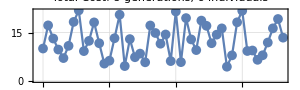

```mathematica
ListLinePlot[Flatten[costTotal2],PlotMarkers->{"●",10},PlotTheme->"Detailed",PlotLabel->Style[StringJoin["Total Cost: ",ToString[nGen-1]," generations, ",ToString[genSize]," individuals"],Bold,13],FrameTicks->{{All,None},{Range[nGen*genSize],None}},ImageSize->{300,100},AspectRatio->3/10]
```

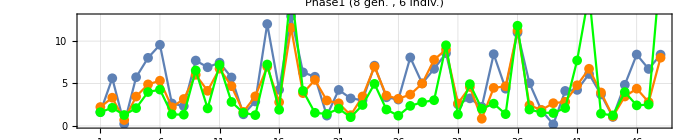

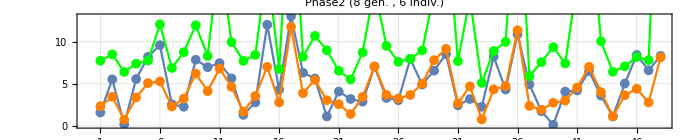

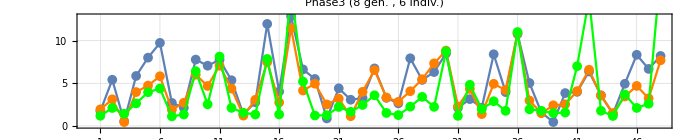

```mathematica
For[phase=1,phase≤ nphase,phase++,
Print[Show[{ListLinePlot[Flatten[errorMtx2[[All,All,phase,1]]]/77,PlotMarkers->{"●",10},PlotTheme->"Detailed",PlotLabel->Style[StringJoin["Phase",ToString[phase]," (",ToString[nGen-1]," gen. , ",ToString[genSize]," indiv.)"],Bold,13],FrameTicks->{{All,None},{Range[nGen*genSize],None}},PlotLegends->Placed[{"1st IntError"},Right],ImageSize->{700,200},AspectRatio->2/10]
,
ListLinePlot[Flatten[errorMtx2[[All,All,phase,2]]]/7.6,PlotMarkers->{"●",10},PlotTheme->"Detailed",FrameTicks->{{All,None},{Range[nGen*genSize],None}},PlotLegends->Placed[{"2nd IntError"},Right],PlotStyle->Orange]
,
ListLinePlot[Flatten[errorMtx2[[All,All,phase,3]]],PlotMarkers->{"●",10},PlotTheme->"Detailed",FrameTicks->{{All,None},{Range[nGen*genSize],None}},PlotLegends->Placed[{"Phase Error"},Right],PlotStyle->Green]
}]]
]
```

## Test Best Individual

```mathematica
(*errorMtx2[[generation,i,phase]]={Int1Error,Int2Error,RootMeanSquare[phError]}*)
(*magMtx2[[i]]={offspring1,offspringIdx1,termination1} = {12,3,4}*)
(*costTotal2[[gen,i]]*)

DumpGet[StringJoin[NotebookDirectory[],"errorMtx2.mx"]];
DumpGet[StringJoin[NotebookDirectory[],"magMtx2.mx"]];
DumpGet[StringJoin[NotebookDirectory[],"costTotal2.mx"]];
```

```mathematica
bestGen=Ordering[Table[Min[costTotal2[[i]]],{i,1,nGen-1}]][[1]];
bestInd=Ordering[costTotal2[[bestGen]]][[1]];

bestMag=magMtx2[[6*(bestGen-1)+bestInd,1]];
bestTerm=magMtx2[[6*(bestGen-1)+bestInd,3]];
bestBlockList=magMtx2[[6*(bestGen-1)+bestInd,2]];

bestIndiv=Join[bestTerm[[All,1,All]],bestMag,bestTerm[[All,4,All]],2];
```

```mathematica
testError=ConstantArray[0,nphase];
testErrorMtx=ConstantArray[0,nphase];

For[phase=1,phase≤nphase,phase++,
(*Draw*)
device=idDraw[typeID="DeltaUndulator",gap,nPeriods,periodL,blockGeo,blockThick,blockGap,bestMag,bestTerm,phase,subdiv ];
(*Solve*)
idSolve[device];
(*Field*)
baxis=idField[device,li,lf,lNpts,{0,0},display=0,oneplot=0];

(*Integral Error*)
integral=idFieldInt[device,li,lf,lstep,baxis,display=0,oneplot=0]; 
Int1Error=Sqrt[((integral[[1,-1,1]])^2+(integral[[1,-1,2]])^2+(integral[[1,-1,3]])^2)/3];
Int2Error=Sqrt[((integral[[2,-1,1]])^2+(integral[[2,-1,2]])^2+(integral[[2,-1,3]])^2)/3];

(*Trajetoria*)
Trajetoria=idTrajectory[device, eEnergy,{0,0,li,0,0,1},lf,lstep,display=0] ;
(*Phase Error*)
phError=idPhaseError[baxis,li,lf,lNpts,Trajetoria,eEnergy];

(*Error Function*)
weight1Int=1/77; weight2Int=1/7.6; weightPh=1;
testError[[phase]]= Int1Error*weight1Int+Int2Error*weight2Int+RootMeanSquare[phError]*weightPh;
testErrorMtx[[phase]]={Int1Error,Int2Error,RootMeanSquare[phError]};

Print[Style["\n>> Cost [Phase ",Bold,13],phase,Style["]: ",Bold,13],testError[[phase]]];
Print["- 1st Integral (Ix,Iy,Iz)[G.cm]:\t",integral[[1,-1]] ];
Print["- 2nd Integral (IIx,IIy,IIz)[G.cm.b2]:\t",integral[[2,-1]] ];
Print["- RMS Phase Error [deg]:\t\t",RootMeanSquare[phError]];


];(*Phase*)

testCost=Sum[testError[[k]],{k,1,nphase}]/nphase;
Print[Style["\n>> Total Cost: ",Bold,14], testCost];
```

>> Cost [Phase 1]: 2.23317

- 1st Integral (Ix,Iy,Iz)[G.cm]:	{-10.6223,28.9203,0.0147436}

- 2nd Integral (IIx,IIy,IIz)[G.cm.b2]:	{9.11025,2.15738,-1.39478}

- RMS Phase Error [deg]:		1.28309

>> Cost [Phase 2]: 7.41337

- 1st Integral (Ix,Iy,Iz)[G.cm]:	{-14.5965,14.3404,0.0747429}

- 2nd Integral (IIx,IIy,IIz)[G.cm.b2]:	{9.29087,2.97956,-1.37178}

- RMS Phase Error [deg]:		6.51144

>> Cost [Phase 3]: 2.39426

- 1st Integral (Ix,Iy,Iz)[G.cm]:	{-67.1213,8.05195,0.264894}

- 2nd Integral (IIx,IIy,IIz)[G.cm.b2]:	{5.34032,-2.60383,-1.33298}

- RMS Phase Error [deg]:		1.4248

>> Total Cost: 4.0136

## Export

```mathematica
fileNameB="Blocks_B_V2.xlsx"; (*Magnetizations File name (with extension)*)
headLineB=1; (*Number of Head Lines on the File*)
fileNameT="Blocks_T_V2.xlsx"; (*Magnetizations File name (with extension)*)
headLineT=1; (*Number of Head Lines on the File*)

listMagB=idSortingImportMag[fileNameB,headLineB];
listMagT=idSortingImportMag[fileNameT,headLineT];
```

```mathematica
magLimit=10^-6;
dir=NotebookDirectory[];

(*Termination Front Index*)
idxTf=Table[Position[listMagT[[All,2]],bestBlockList[[j,i]]][[1,1]],{j,1,Length[bestBlockList]},{i,1,Length[bestTerm[[1,1]]]}];
(*Normal Size Blocks Index*)
idxb=Table[Position[listMagB[[All,2]],bestBlockList[[j,i]]][[1,1]],{j,1,Length[bestBlockList]},{i,Length[bestTerm[[1,1]]]+1,Length[bestBlockList[[1]]]-Length[bestTerm[[1,1]]]}];
(*Termination Back Index*)
idxTb=Table[Position[listMagT[[All,2]],bestBlockList[[j,i]]][[1,1]],{j,1,Length[bestBlockList]},{i,-Length[bestTerm[[1,1]]],-1}];

idx=Join[idxTf,idxb,idxTb,2];
```

```mathematica
(*Termination Front Rotation Indicative*)
diffTf=Table[listMagT[[idxTf[[j,i]],1]]-bestTerm[[j,1,i]],{j,1,Length[idxTf]},{i,1,Length[idxTf[[1]]]}];
(*Normal Size Blocks Rotation Indicative*)
diffb=Table[listMagB[[idxb[[j,i]],1]]-bestMag[[j,i]],{j,1,Length[idxb]},{i,1,Length[idxb[[1]]]}];
(*Termination Back Rotation Indicative*)
diffTb=Table[listMagT[[idxTb[[j,i]],1]]-bestTerm[[j,1,i]],{j,1,Length[idxTb]},{i,1,Length[idxTb[[1]]]}];

diff=Join[diffTf,diffb,diffTb,2];
```

```mathematica
(*Create a matrix with 1 for rotated blocks, and 0 for unrotated blocks*)
rotateIdx=Table[If[Abs[diff[[j,i,1]]]<magLimit,0,1],{j,1,Length[diff]},{i,1,Length[diff[[1]]]}];
```

```mathematica
(* Create Result Matrix *)
resultCass=Table[Join[{bestBlockList[[j,i]]},bestIndiv[[j,i]],{rotateIdx[[j,i]]}],{j,1,Length[bestIndiv]},{i,1,Length[bestIndiv[[1]]]}];
```

```mathematica
Export[StringJoin[dir,"Sorting_Otimization_Result.xlsx"],{"Cassete ID"-> resultCass[[1]],"Cassete IE"->resultCass[[2]],"Cassete SE"->resultCass[[3]],"Cassete SD"->resultCass[[4]]}];
```